```mathematica
Needs["dsvsolve`"];
```

## Input

Edit or simply evaluate the following cell to see the input

General::compat: Combinatorica Graph and Permutations functionality has been superseded by preloaded functionality. The package now being loaded may conflict with this. Please see the Compatibility Guide for details.

BFShowInput::assm: Assumptions made: {L→0.75,q→0.09,αΔT→0.08}.

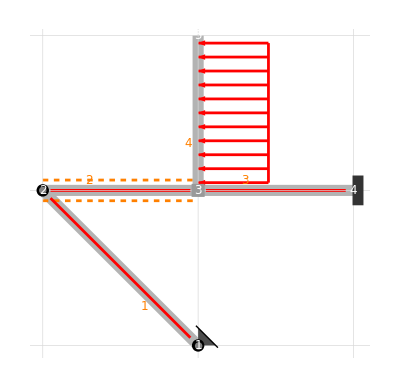

```mathematica
example={$$nodes->{{0, -L}, {-L, 0}, {0, 0}, {L, 0}, {0, L}},
$$edges->{{1, 2}, {2, 3}, {3, 4}, {3, 5}},$$absname->s,
$$constraints->{{{"hinge", 1}}, {{"hinge", 1, 2}}, {{"clamp", 2, 3}, {"clamp", 3, 4}}, {{"clamp", 3}}, {{"free", 4}}},
$$bodyloads->{{4, {0, q, 0}}},
$$nodalloads->{},
$$predeformations->{{2, {αΔT, 0, 0}}},
$$cdisplacements->{{1, {0, 0, 0}}},
$$EIoverEAL2->0};
(*All constraints are initialized to hinge constraints; use "BFConstraintsPalette[BFConstraintTypes];" to input different constraints.*)
BFShowInput[example]
```

## Output

Evaluate the following cell to solve the problem and see the output

```mathematica
BFClassify[example]; sol = {{Ns, Qs, Ms}, details} = BFForcesSolve[example,13];
(*A=Transpose[First[BFStaticProblem[example]]];MatrixForm[A]
BFShowRigidMotions[example]*)
(*BFEquations[example,"Nodal"]; sol = {{us, vs}, {Ns, Qs, Ms}, details} = BFDisplacementsSolve[example];*)
gsol=BFShowOutput[example, sol]
```

BFClassify::su: Statically undetermined system of order 1.
13 possible choices of static unknows are as follows:
1
N_1[0] | 2
N_1[1] | 3
N_2[0] | 4
Q_2[0] | 5
N_2[1] | 6
Q_2[1] | 7
M_2[1] | 8
N_3[0] | 9
Q_3[0] | 10
M_3[0]
11
N_3[1] | 12
Q_3[1] | 13
M_3[1] |   |   |   |   |   |   |

BFClassify::kd: Kinematically determined system.

BFForcesSolve::suc: Chosen set of static unknows: {M_3[1]}

12345

Evaluate the following cell to print the above output

```mathematica
CellPrint/@Rest/@Last[sol];
Print/@Cases[gsol,Graphics[___],Infinity];
```

Dimensionless abscissa

s

Static equilibrium matrix

{{-1,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,-1,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,-1,0,√2 L,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,-1,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,-1,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,-1,0,L,1,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,-1,0,0,1,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,-1,0,0,1,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1,0,L,1,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1,0,0,1,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1,0,0,1,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1,0,L,1},{0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,√2,√2,0,2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,-√2,√2,0,0,2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,-1,0,0,1,0,0,0,0,0,0,-1,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,-1,0,0,1,0,0,0,0,1,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,-1,0,0,1,0,0,0,0,0,1,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1}}

Static equilibrium vector

{0,0,0,0,0,0,0,0,0,0,-L q,-(L^2 q)/2,0,0,0,0,0,0,0,0,0,0,0}

Fredholm condition: are the loads orthogonal to allowed rigid motions?

True

Bending stiffnesses

{EI,EI,EI,EI}

Axial stiffnesses

{∞,∞,∞,∞}

Degree of static undetermination

1

Some possible choices for the static unknowns

{{("N")_("1")[0]},{("N")_("1")[1]},{("N")_("2")[0]},{("Q")_("2")[0]},{("N")_("2")[1]},{("Q")_("2")[1]},{("M")_("2")[1]},{("N")_("3")[0]},{("Q")_("3")[0]},{("M")_("3")[0]},{("N")_("3")[1]},{("Q")_("3")[1]},{("M")_("3")[1]}}

Actually chosen static unknowns

{("M")_("3")[1]}

Reactions in the auxiliary problem 0

{{-(L q)/(2 √2),0,0,-(L q)/(2 √2),0,0},{(L q)/4,-(L q)/4,0,(L q)/4,-(L q)/4,(L^2 q)/4},{(5 L q)/4,-(L q)/4,-(L^2 q)/4,(5 L q)/4,-(L q)/4,0},{0,L q,(L^2 q)/2,0,0,0}}

Reactions in the auxiliary problem 1

{{-1/(√2 L),0,0,-1/(√2 L),0,0},{1/(2 L),-1/(2 L),0,1/(2 L),-1/(2 L),1/2},{1/(2 L),-1/(2 L),1/2,1/(2 L),-1/(2 L),1},{0,0,0,0,0,0}}

Internal actions (N,Q,M) in the auxiliary problem 0

{{-(L q)/(2 √2),(L q)/4,(5 L q)/4,0},{0,-(L q)/4,-(L q)/4,-L q (-1+s)},{0,1/4 L^2 q s,1/4 L^2 q (-1+s),1/2 L^2 q (-1+s)^2}}

Internal actions (N,Q,M) in the auxiliary problem 1

{{-1/(√2 L),1/(2 L),1/(2 L),0},{0,-1/(2 L),-1/(2 L),0},{0,s/2,(1+s)/2,0}}

Mohr's Integrals: coefficient matrix ηij

{{(2 L)/(3 EI)}}

Mohr's Integrals: vector ηi0

{-(L^3 q)/(24 EI)+αΔT/2}

Mohr's Integrals: solution for the static unknowns

{("M")_("3")[1]→(L^3 q-12 EI αΔT)/(16 L)}

Actual reactions

{{(3 (-3 L^3 q+4 EI αΔT))/(16 √2 L^2),0,0,(3 (-3 L^3 q+4 EI αΔT))/(16 √2 L^2),0,0},{(9 L q)/32-(3 EI αΔT)/(8 L^2),-(9 L q)/32+(3 EI αΔT)/(8 L^2),0,(9 L q)/32-(3 EI αΔT)/(8 L^2),-(9 L q)/32+(3 EI αΔT)/(8 L^2),(3 (3 L^3 q-4 EI αΔT))/(32 L)},{(41 L q)/32-(3 EI αΔT)/(8 L^2),-(9 L q)/32+(3 EI αΔT)/(8 L^2),-(7 L^3 q+12 EI αΔT)/(32 L),(41 L q)/32-(3 EI αΔT)/(8 L^2),-(9 L q)/32+(3 EI αΔT)/(8 L^2),(L^3 q-12 EI αΔT)/(16 L)},{0,L q,(L^2 q)/2,0,0,0}}

Actual internal actions (N,Q,M)

{{(3 (-3 L^3 q+4 EI αΔT))/(16 √2 L^2),(9 L q)/32-(3 EI αΔT)/(8 L^2),(41 L q)/32-(3 EI αΔT)/(8 L^2),0},{0,-(9 L q)/32+(3 EI αΔT)/(8 L^2),-(9 L q)/32+(3 EI αΔT)/(8 L^2),-L q (-1+s)},{0,(3 s (3 L^3 q-4 EI αΔT))/(32 L),(L^3 q (-7+9 s)-12 EI (1+s) αΔT)/(32 L),1/2 L^2 q (-1+s)^2}}

-Graphics-

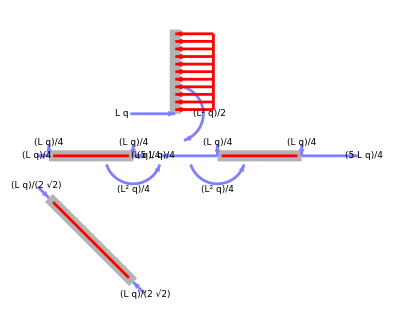

-Graphics-

-Graphics-

-Graphics-

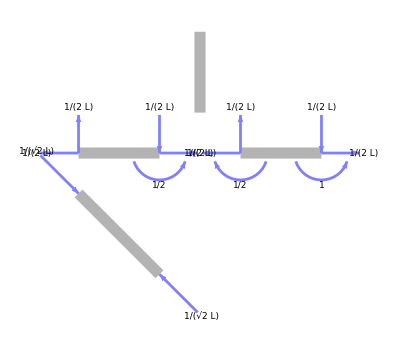

-Graphics-

-Graphics-

-Graphics-

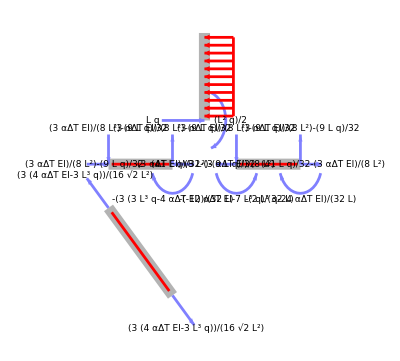

-Graphics-

-Graphics-

-Graphics-